## Functions

```mathematica
Quit[]
```

```mathematica
NearZero[s_]:=Abs[s]<10^-6
TransToRp[T_]:={T[[1;;3,1;;3]],{T[[1;;3,4]]}ᵀ};
TransInv[T_]:=
ArrayFlatten[{{T[[1;;3,1;;3]]ᵀ,-T[[1;;3,1;;3]]ᵀ.{T[[1;;3,4]]}ᵀ},{0,1}}]
se3ToVec[se3mat_]:={{se3mat[[3,2]],se3mat[[1,3]],se3mat[[2,1]],se3mat[[1,4]],se3mat[[2,4]],se3mat[[3,4]]}}ᵀ
so3ToVec[so3mat_]:={{so3mat[[3,2]],so3mat[[1,3]],so3mat[[2,1]]}}ᵀ
VecToso3[omg_]:={{0,-omg[[3,1]],omg[[2,1]]},{omg[[3,1]],0,-omg[[1,1]]},{-omg[[2,1]],omg[[1,1]],0}}
VecTose3[V_]:=ArrayFlatten[{{VecToso3[{V[[1;;3,1]]}ᵀ],{V[[4;;6,1]]}ᵀ},{0,0}}]
AxisAng3[expc3_]:={expc3/Norm[expc3],Norm[expc3]}
MatrixExp3[so3mat_]:=Module[{omgtheta,omghat,theta,omgmat},omgtheta=so3ToVec[so3mat];If[NearZero[Norm[omgtheta]],Return[IdentityMatrix[3]],{omghat, theta} = AxisAng3[omgtheta];omgmat=so3mat/theta;Return[IdentityMatrix[3]+Sin[theta]*omgmat+(1-Cos[theta])*omgmat.omgmat]]]
MatrixLog3[R_]:=Module[{acosinput,theta,omgmat},Which[NearZero[Norm[R-IdentityMatrix[3]]],Return[ConstantArray[0,{3,3}]],NearZero[Tr[R]+1],Which[Not[NearZero[R[[3,3]]+1]],Return[VecToso3[1/Sqrt[2(1+R[[3,3]])]*{{R[[1,3]],R[[2,3]],1+R[[3,3]]}}ᵀ*Pi]],Not[NearZero[R[[2,2]]+1]],Return[VecToso3[1/Sqrt[2(1+R[[2,2]])]*{{R[[1,2]],1+R[[2,2]],R[[3,2]]}}ᵀ*Pi]],True,Return[VecToso3[1/Sqrt[2(1+R[[1,1]])]*{{1+R[[1,1]],R[[2,1]],R[[3,1]]}}ᵀ*Pi]]],True,acosinput=(Tr[R]-1)/2;Which[acosinput>1,acosinput=1,acosinput<-1,acosinput=-1];theta=ArcCos[acosinput];omgmat=(R-Rᵀ)/(2*Sin[theta]);Return[theta*omgmat]]]
MatrixExp6[se3mat_]:=Module[{omgtheta,omghat,theta,omgmat,G},omgtheta=so3ToVec[se3mat[[1;;3,1;;3]]];If[NearZero[Norm[omgtheta]],Return[ArrayFlatten[{{IdentityMatrix[3],{se3mat[[1;;3,4]]}ᵀ},{0,1}}]],{omghat,theta} = AxisAng3[omgtheta];omgmat=se3mat[[1;;3,1;;3]]/theta;Return[ArrayFlatten[{{MatrixExp3[se3mat[[1;;3,1;;3]]],(IdentityMatrix[3]*theta+(1-Cos[theta])*omgmat+(theta-Sin[theta])*omgmat.omgmat).({se3mat[[1;;3,4]]}ᵀ/theta)},{0,1}}]]]]
MatrixLog6[T_]:=Module[{R,p,acosinput,theta,omgmat},{R,p}=TransToRp[T];If[NearZero[Norm[R-IdentityMatrix[3]]],ArrayFlatten[{{ConstantArray[0,{3,3}],{T[[1;;3,4]]}ᵀ},{0,0}}],acosinput=(Tr[R]-1)/2;Which[acosinput>1,acosinput=1,acosinput<-1,acosinput=-1];theta=ArcCos[acosinput];omgmat=MatrixLog3[R];Return[ArrayFlatten[{{omgmat,(IdentityMatrix[3]-omgmat/2+(1/theta-Cot[theta/2]/2)*omgmat.omgmat/theta).p},{0,0}}]]]]
JacobianSpace[Slist_,thetalist_]:=Module[{Js=Slist,T=IdentityMatrix[4]},Do[T=T.MatrixExp6[VecTose3[{Slist[[;;,i-1]]}ᵀ*thetalist[[i-1,1]]]];Js[[;;,i]]=Flatten[Adjoint[T].{Slist[[;;,i]]}ᵀ],{i,2,Length[thetalist]}];Return[Js]]
JacobianBody[Blist_,thetalist_]:=Module[{Jb=Blist,T=IdentityMatrix[4]},Do[T=T.MatrixExp6[VecTose3[{Blist[[;;,i+1]]}ᵀ*-thetalist[[i+1,1]]]];Jb[[;;,i]]=Flatten[Adjoint[T].{Blist[[;;,i]]}ᵀ],{i,Length[thetalist]-1,1,-1}];Return[Jb]]
FKinBody[M_,Blist_,thetalist_]:=Module[{n,T,i},T=M;Do[T=T.MatrixExp6[VecTose3[{Blist[[;;,i]]}ᵀ*thetalist[[i,1]]]],{i,Length[thetalist]}];
Return[T]]
FKinSpace[M_,Slist_,thetalist_]:=Module[{n,T},T=M;Do[T=MatrixExp6[VecTose3[{Slist[[;;,i]]}ᵀ*thetalist[[i,1]]]].T,{i,Length[thetalist],1,-1}];
Return[T]]
Adjoint[T_]:=Module[{R,p},{R,p}=TransToRp[T];Return[ArrayFlatten[{{R,0},{VecToso3[p].R,R}}]]]
IKinBody[Blist_,M_,T_,thetalist0_,eomg_,ev_]:=Module[{Vb,thetalist=thetalist0,err,i=0,maxiterations = 20},Vb = se3ToVec[MatrixLog6[TransInv[FKinBody[M,Blist,thetalist]].T]];
err=Norm[Vb[[1;;3,1]]]>eomg || Norm[Vb[[4;;6,1]]]>ev;
While[err &&i < maxiterations,thetalist= thetalist+PseudoInverse[JacobianBody[Blist,thetalist]].Vb;i++;Vb = se3ToVec[MatrixLog6[TransInv[FKinBody[M,Blist,thetalist]].T]];
err=Norm[Vb[[1;;3,1]]]>eomg || Norm[Vb[[4;;6,1]]]>ev];
Return[{thetalist, !err}]]
FKinBody[M_,Blist_,thetalist_]:=Module[{n,T,i},T=M;Do[T=T.MatrixExp6[VecTose3[{Blist[[;;,i]]}ᵀ*thetalist[[i,1]]]],{i,Length[thetalist]}];
Return[T]]
```

## Part (c)

```mathematica
Blist={{0,0,1,0,0.0330+0.1662,0},{0,0,0,1,0,0},{0,0,0,0,1,0},{0,0,1,0,0.0330,0},{0,-1,0,-0.5076,0,0},{0,-1,0,-0.3526,0,0},{0,-1,0,-0.2176,0,0},{0,0,1,0,0,0}}ᵀ;
M={{1,0,0,0.0330+0.1662},{0,1,0,0},{0,0,1,0.0026+0.0963+0.6546},{0,0,0,1}}; 
T = {{0,0,0,0},{0,0,1,1},{0,-1,0,0.4},{0,0,0,1}};thetalist0={{0,0,0,0,0,-π/2,0,0}}ᵀ;
eomg=0.01;
ev=0.001;
{thetalist,success} = IKinBody[Blist,M,T,thetalist0,eomg,ev];
Print[" The chassis and arm configuration that places the end effector is (ϕ,x,y,θ1,θ2,θ3,θ4,θ5): ",MatrixForm[thetalist]];
Print[" \nThe end effector configuration is : ",MatrixForm[Chop[FKinBody[M,Blist,thetalist],0.01]]];
```

The chassis and arm configuration that places the end effector is (ϕ,x,y,θ1,θ2,θ3,θ4,θ5): (0.862239
0.332641
0.429068
0.705106
0.284306
4.46752
-6.32262
-1.56735)

The end effector configuration is : (0.999988 | 0 | 0 | 0
0 | 0 | 0.999994 | 0.999999
0 | -0.999994 | 0 | 0.400001
0 | 0 | 0 | 1.)

## Part (d)

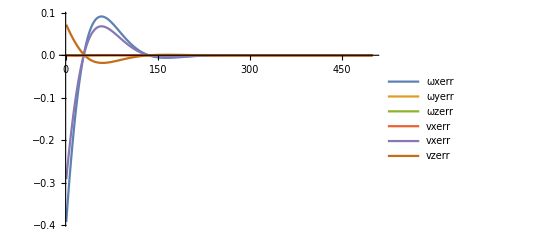

```mathematica
(*Setup*)
Tsb = {{Cos[ϕ],-Sin[ϕ],0,x},{Sin[ϕ],Cos[ϕ],0,y},{0,0,1,0.0963},{0,0,0,1}};
s[t_] = (3/25)t^2 - (2/125)*t^3;
Xd={{Sin[s[t]*π/2],0,Cos[s[t]*π/2],s[t]},{0,1,0,0},{-Cos[s[t]*π/2],0,Sin[s[t]*π/2],0.491},{0,0,0,1}};
q0={{-π/8,-0.5,0.5}}ᵀ; 
(*q0={{0,-0.526,0}}ᵀ;*)
theta0 = {{0,-π/4,π/4,-π/2,0}}ᵀ;
w0={{0,0,0,0}}ᵀ;
Blist={{0,0,1,0,0.0330,0},{0,−1,0,−0.5076,0,0},{0,-1,0,−0.3526,0,0},{0,-1,0,−0.2176,0,0},{0,0,1,0,0,0}}ᵀ;
Totalerror ={{0},{0},{0},{0},{0},{0}};
Kp =5;
Ki=15;
mat =List[];
Xerrmat1 = List[];
Xerrmat2 = List[];
Xerrmat3 = List[];
Xerrmat4 = List[];
Xerrmat5 = List[];
Xerrmat6 = List[];
For[i=1;dt=0,i≤500,dt=dt+0.01;i=i+1,
(* Get Xd and Vd at the Current Time*)
Xdval = Xd/.t->dt;
Vd =se3ToVec[Inverse[Xdval].D[Xd,t]]//FullSimplify;
Vdval = Vd/.t->dt;
(*Calculate the configuration error*)
Moe = {{1,0,0,0.0330},{0,1,0,0},{0,0,1,0.6546},{0,0,0,1}};
Tbo= {{1,0,0,0.1662},{0,1,0,0},{0,0,1,0.0026},{0,0,0,1}};
Toe =FKinBody[Moe,Blist,theta0];
Tsbval = Tsb/.{ϕ->q0[[1,1]],x->q0[[2,1]],y->q0[[3,1]]};
X=Tsbval.Tbo.Toe;
Xerr =se3ToVec[ MatrixLog6[Inverse[X].Xdval]];
Xerrmat1 = Append[Xerrmat1,Xerr[[1,1]]];
Xerrmat2 = Append[Xerrmat2,Xerr[[2,1]]];
Xerrmat3 = Append[Xerrmat3,Xerr[[3,1]]];
Xerrmat4 = Append[Xerrmat4,Xerr[[4,1]]];
Xerrmat5 = Append[Xerrmat5,Xerr[[5,1]]];
Xerrmat6 = Append[Xerrmat6,Xerr[[6,1]]];
(*Evaluate the control law*)
Totalerror = Totalerror + Xerr*0.01;
V = (Adjoint[Inverse[X].Xdval].Vdval) + Kp*Xerr + Ki*Totalerror;
(*Update velocities of the joints and the wheels*)
l=0.47/2;
w=0.3/2;
r = 0.0475;
F =r/4* {{-1/(l+w),1/(l+w),1/(l+w),-1/(l+w)},{1,1,1,1},{-1,1,-1,1}};
F6 = ArrayFlatten[{{0},{0},{F},{0}}];
Jbase = Adjoint[Inverse[Toe].Inverse[Tbo]].F6;
Jarm =JacobianBody[Blist,theta0];
Je = Join[Jbaseᵀ,Jarmᵀ]ᵀ;
A = PseudoInverse[Je].V;
u = {A[[1]],A[[2]],A[[3]],A[[4]]};
thetadot =  {A[[5]],A[[6]],A[[7]],A[[8]],A[[9]]};
(*Simulate the next step*)
 Vb = F.(u*0.01);
If[Vb[[1,1]]==0,
delϕ = Vb[[1,1]];delx = Vb[[2,1]];dely = Vb[[3,1]],
delϕ = Vb[[1,1]];delx = ((Vb[[2,1]]*Sin[Vb[[1,1]]])+(Vb[[3,1]]*(Cos[Vb[[1,1]]]-1)))/Vb[[1,1]];dely = ((Vb[[3,1]]*Sin[Vb[[1,1]]])+(Vb[[2,1]]*(1-Cos[Vb[[1,1]]])))/Vb[[1,1]];];
delqb = {delϕ,delx,dely};
delq = {{1,0,0},{0,Cos[q0[[1,1]]],-Sin[q0[[1,1]]]},{0,Sin[q0[[1,1]]],Cos[q0[[1,1]]]}}.delqb;
q0 = q0 + delq;
theta0 = theta0+thetadot*0.01 ;
q0list = {q0[[2]],q0[[3]],q0[[1]]};
w0 = w0 + u*0.01;
JoinedList =Join[q0list,theta0,w0]ᵀ;
mat = Append[mat,JoinedList[[1]]];]
Export["Kuka.csv",mat];
ListLinePlot[{Xerrmat1,Xerrmat2,Xerrmat3,Xerrmat4,Xerrmat5,Xerrmat6},PlotLegends->{"ωxerr","ωyerr","ωzerr","vxerr","vxerr","vzerr"},PlotRange->All]
```

## Part (e)

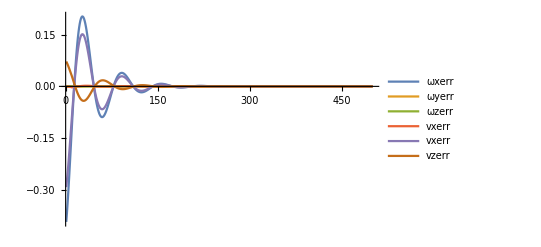

```mathematica
(*Setup*)
Tsb = {{Cos[ϕ],-Sin[ϕ],0,x},{Sin[ϕ],Cos[ϕ],0,y},{0,0,1,0.0963},{0,0,0,1}};
s[t_] = (3/25)t^2 - (2/125)*t^3;
Xd={{Sin[s[t]*π/2],0,Cos[s[t]*π/2],s[t]},{0,1,0,0},{-Cos[s[t]*π/2],0,Sin[s[t]*π/2],0.491},{0,0,0,1}};
q0={{-π/8,-0.5,0.5}}ᵀ; 
(*q0={{0,-0.526,0}}ᵀ;*)
theta0 = {{0,-π/4,π/4,-π/2,0}}ᵀ;
w0={{0,0,0,0}}ᵀ;
Blist={{0,0,1,0,0.0330,0},{0,−1,0,−0.5076,0,0},{0,-1,0,−0.3526,0,0},{0,-1,0,−0.2176,0,0},{0,0,1,0,0,0}}ᵀ;
Totalerror ={{0},{0},{0},{0},{0},{0}};
Kp =5;
Ki=100;
mat =List[];
Xerrmat1 = List[];
Xerrmat2 = List[];
Xerrmat3 = List[];
Xerrmat4 = List[];
Xerrmat5 = List[];
Xerrmat6 = List[];
For[i=1;dt=0,i≤500,dt=dt+0.01;i=i+1,
(* Get Xd and Vd at the Current Time*)
Xdval = Xd/.t->dt;
Vd =se3ToVec[Inverse[Xdval].D[Xd,t]]//FullSimplify;
Vdval = Vd/.t->dt;
(*Calculate the configuration error*)
Moe = {{1,0,0,0.0330},{0,1,0,0},{0,0,1,0.6546},{0,0,0,1}};
Tbo= {{1,0,0,0.1662},{0,1,0,0},{0,0,1,0.0026},{0,0,0,1}};
Toe =FKinBody[Moe,Blist,theta0];
Tsbval = Tsb/.{ϕ->q0[[1,1]],x->q0[[2,1]],y->q0[[3,1]]};
X=Tsbval.Tbo.Toe;
Xerr =se3ToVec[ MatrixLog6[Inverse[X].Xdval]];
Xerrmat1 = Append[Xerrmat1,Xerr[[1,1]]];
Xerrmat2 = Append[Xerrmat2,Xerr[[2,1]]];
Xerrmat3 = Append[Xerrmat3,Xerr[[3,1]]];
Xerrmat4 = Append[Xerrmat4,Xerr[[4,1]]];
Xerrmat5 = Append[Xerrmat5,Xerr[[5,1]]];
Xerrmat6 = Append[Xerrmat6,Xerr[[6,1]]];
(*Evaluate the control law*)
Totalerror = Totalerror + Xerr*0.01;
V = (Adjoint[Inverse[X].Xdval].Vdval) + Kp*Xerr + Ki*Totalerror;
(*Update velocities of the joints and the wheels*)
l=0.47/2;
w=0.3/2;
r = 0.0475;
F =r/4* {{-1/(l+w),1/(l+w),1/(l+w),-1/(l+w)},{1,1,1,1},{-1,1,-1,1}};
F6 = ArrayFlatten[{{0},{0},{F},{0}}];
Jbase = Adjoint[Inverse[Toe].Inverse[Tbo]].F6;
Jarm =JacobianBody[Blist,theta0];
Je = Join[Jbaseᵀ,Jarmᵀ]ᵀ;
A = PseudoInverse[Je].V;
u = {A[[1]],A[[2]],A[[3]],A[[4]]};
thetadot =  {A[[5]],A[[6]],A[[7]],A[[8]],A[[9]]};
(*Simulate the next step*)
 Vb = F.(u*0.01);
If[Vb[[1,1]]==0,
delϕ = Vb[[1,1]];delx = Vb[[2,1]];dely = Vb[[3,1]],
delϕ = Vb[[1,1]];delx = ((Vb[[2,1]]*Sin[Vb[[1,1]]])+(Vb[[3,1]]*(Cos[Vb[[1,1]]]-1)))/Vb[[1,1]];dely = ((Vb[[3,1]]*Sin[Vb[[1,1]]])+(Vb[[2,1]]*(1-Cos[Vb[[1,1]]])))/Vb[[1,1]];];
delqb = {delϕ,delx,dely};
delq = {{1,0,0},{0,Cos[q0[[1,1]]],-Sin[q0[[1,1]]]},{0,Sin[q0[[1,1]]],Cos[q0[[1,1]]]}}.delqb;
q0 = q0 + delq;
theta0 = theta0+thetadot*0.01 ;
q0list = {q0[[2]],q0[[3]],q0[[1]]};
w0 = w0 + u*0.01;
JoinedList =Join[q0list,theta0,w0]ᵀ;
mat = Append[mat,JoinedList[[1]]];]
Export["Kuka.csv",mat];
ListLinePlot[{Xerrmat1,Xerrmat2,Xerrmat3,Xerrmat4,Xerrmat5,Xerrmat6},PlotLegends->{"ωxerr","ωyerr","ωzerr","vxerr","vxerr","vzerr"},PlotRange->All]
```